```mathematica
<<Topy/vizhandmap.m
```

```mathematica
<<Topy/polygongeometry.m
```

```mathematica
<<Topy/projections.m
```

## Code

```mathematica
(* f is a function taking a polygon *)
colorValues[data_,f_]:=
Module[{zz,zzz,zzzz},
zz=rfCoords[
data,
CoordIndex1->-2,
CoordsOnly->True,
OutputInRad->True];
zzz=Map[Partition[#,2]&,zz];
zzzz=Map[f,zzz];
Return[zzzz]
]
```

## Use

```mathematica
data1=Import["/Users/work/website/visuotopy/data/mk9RFS-edited2.txt",
"Table"];
```

```mathematica
data2=Import["/Users/work/website/visuotopy/data/CJ119RFs-edit2.txt",
"Table"];
```

```mathematica
cf=ColorData["DarkRainbow"];
```

```mathematica
colors1=Table[cf[Random[]],{Length[data1]}];
```

```mathematica
colors2=Table[cf[Random[]],{Length[Select[data2,#[[-1]]=="V1"&]]}];
```

```mathematica
g1a=vizHandmap1[
data1,
CoordIndex1->-2,
LongitudeRange->{-90Degree,90Degree},
ImageSize->200,
PolygonColorFunc->colors1,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
];
```

```mathematica
g1b=vizHandmap1[
data1,
CoordIndex1->-2,
LongitudeRange->{-90Degree,90Degree},
ImageSize->200,
PolygonColorFunc->colors1,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}],
ProjectionFunc->sphericalProjectionFunction["stereographic"]
];
```

```mathematica
g2a=vizHandmap1[
data2,
CoordIndex1->-2,
LongitudeRange->{-90Degree,90Degree},
ImageSize->200,
RFFilterFunc->Function[{x},x[[-1]]=="V1"],
DisplayBackground->False,
PolygonColorFunc->colors2,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
];
```

```mathematica
g2b=vizHandmap1[
data2,
CoordIndex1->-2,
LongitudeRange->{-90Degree,90Degree},
ImageSize->200,
RFFilterFunc->Function[{x},x[[-1]]=="V1"],
DisplayBackground->False,
PolygonColorFunc->colors2,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}],
ProjectionFunc->sphericalProjectionFunction["stereographic"]
];
```

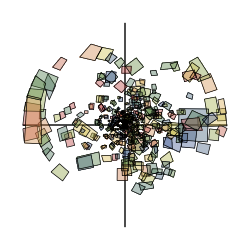

```mathematica
Show[g1a,g2a,ImageSize->250]
```

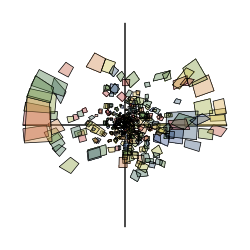

```mathematica
Show[g1b,g2b,ImageSize->250]
```

```mathematica
Export["~/Desktop/proj.png",zz,ImageResolution->200]
```

~/Desktop/proj.png